```mathematica
(*Set the working directory as the directory that the notebook lives in.*)
SetDirectory[NotebookDirectory[]]
```

/Users/junchenrong/Documents/MPS/hard_boson_Rydberg/sample_the_vacuum_state

```mathematica
(*We have collected 1000000 samples using ITensor, we need to import them to mathematica*)
temp=Import["file.txt","String"];
data=temp//StringReplace[#,{"Any"->"","["->"{","]"->"}"}]&//ToExpression;
```

```mathematica
(*Check the size of the sample*)
data//Length
```

1000000

```mathematica
Clear[σσ2pt,md]
(*Since we are dealing with periodic boundary condition, we need to properly deal with the site index*)
md[i_]:=Mod[i-1,40]+1

(*The following function allows us to measue ⟨σ(i)σ(j)⟩ on a specific sample*)
σσ2pt[sp_,i_,j_]:=Module[{},
(-1)^i(-1)^j(sp[[md[i]]]-sp[[md[i+1]]])(sp[[md[j]]]-sp[[md[j+1]]])
]
```

## Measure ⟨σσ⟩ two point function---N=1000

```mathematica
(*We now pick N samples randomly from the large sample pool, here N=1000*)
sample=Module[{data2={}},
Do[
data2=Append[data2,data[[RandomInteger[{1,Length[data]}]]]]
,1000];
data2
];
sample=sample//N;
```

```mathematica
(*We generate all the possible pairs of {i,j} so that the sites are seperated by distance l.*)
Clear[confs]
confs[l_]:=DeleteDuplicates[Sort/@Table[{md[i],md[i+l]},{i,1,40}]]
```

```mathematica
(*This is an auxilary function, it generates out ⟨σ(i)σ(j)⟩ on a single sample, measure on a set of {i,j} pairs*)
Clear[auxσσ2pt]
auxσσ2pt[sp_,confset_]:=Module[{},
σσ2pt[sp,#[[1]],#[[2]]]&/@confset
]
```

```mathematica
L=40;
```

{0.998972,1.99179,2.97232,3.93453,4.87248,5.78039,6.65266,7.48391,8.26903,9.00316,9.68179,10.3007,10.8562,11.3446,11.7632,12.1092,12.3806,12.5756,12.6931,12.7324}

```mathematica
(*x is the conformal distance*)
x=(L/π)Sin[# π/L]&/@Table[l,{l,1,20}]//N;


y=(1.7650291246125218)Table[Mean[(Mean[auxσσ2pt[#,confs[l]]]&/@sample)],{l,1,20}];
(*
"Mean[auxσσ2pt[#,confs[l]]]"

is to measure the ⟨σ(i)σ(j)⟩ with all equavalent {i,j} parirs and then take average,

"(Mean[auxσσ2pt[#,confs[l]]]&/@sample)"
means that we do it on all samples,

"Mean[(Mean[auxσσ2pt[#,confs[l]]]&/@sample)]"
We take the average over all sample.

1.7650291246125218 is c1^2 as defined in the note, value taken from DMRG.
*)



dy=(1.7650291246125218)1/(√1000)Table[StandardDeviation[(Mean[auxσσ2pt[#,confs[l]]]&/@sample)],{l,1,20}];

data$temp=MapThread[{#1,Around[#2,#3]}&,{x,y,dy}];
```

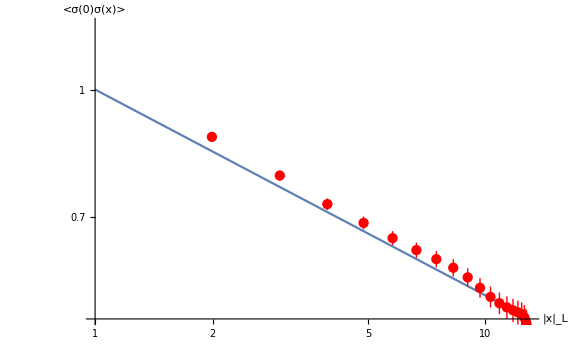

```mathematica
g=Show[LogLogPlot[1/y^(1/4),{y,1,13},PlotRange->{Automatic,{0,1.2}},AxesLabel->{"|x|_L","<σ(0)σ(x)>"}],ListLogLogPlot[data$temp[[2;;20]],(*draw error bars*)IntervalMarkersStyle->Automatic,PlotRange->All,AxesLabel->{"x","y"},PlotStyle->Red],AxesStyle->Large,ImageSize->Large]
```